# Trait-Based Lotka-Volterra Predator-Prey

The trait-based Lotka-Volterra predator-prey model adds a trophic level to the trait-based Lotka-Volterra competition model.

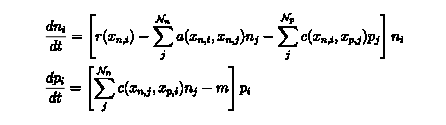

As in the trait-based Lotka-Volterra competition model, k[xn_i] describes the unimodal trait-dependence of the carrying capacity and a[xn_i,xn_j] describes how the strength of competition depends on the difference between species traits, assumed to be a Gaussian function of the trait differences with width σ.  In addition c[xn_i,xp_j] describes how predation depends on predator and prey traits, another Gaussian function of the trait differences with width σc.

-Graphics-

```mathematica
Needs["EcoEvo`"];
```

Set up model:

```mathematica
SetModel[{
Guild[n]->{
Equation:>(r[Subscript[xn, i]]-Sum[a[Subscript[xn, i],Subscript[xn, j]] Subscript[n, j],{j,Subscript[𝒩, n]}]-Sum[c[Subscript[xn, i],Subscript[xp, j]] Subscript[p, j],{j,Subscript[𝒩, p]}])Subscript[n, i],
Traits->{-1≤xn≤1}},
Guild[p]->{
Equation:>(Sum[c[Subscript[xn, j],Subscript[xp, i]] Subscript[n, j],{j,Subscript[𝒩, n]}]-m)Subscript[p, i],
Traits->{-1≤xp≤1}},
Parameters:>{σ>0,σc>0,m>0}
}];
```

```mathematica
a[xi_,xj_]:=E^(-(xi-xj)^2/(2σ^2));
c[xi_,xj_]:=E^(-(xi-xj)^2/(2σc^2));
r[x_]:=1-x^2;
```

Let's start with some analytical work.  Find the one-prey, one-predator ecological equilibria, then find the one-species evolutionary equilibrium:

```mathematica
eq1=SolveEcoEq[{Subscript[𝒩, n]->1,Subscript[𝒩, p]->1}]⟦-1⟧
```

{n_1→ⅇ^((xn_1-xp_1)^2/(2 σc^2)) m,p_1→-ⅇ^((xn_1-xp_1)^2/(2 σc^2)) (-1+ⅇ^((xn_1-xp_1)^2/(2 σc^2)) m+xn_1^2)}

```mathematica
evoeq=FindEvoEq[eq1]
```

{xn_1→0,xp_1→0}

Now check convergence stability with EvoEigenvalues:

```mathematica
EvoEigenvalues[evoeq,eq1]
```

{(1-2 m-2 σc^2-√(1-4 m+4 m^2-4 σc^2+4 σc^4))/(2 σc^2),(1-2 m-2 σc^2+√(1-4 m+4 m^2-4 σc^2+4 σc^4))/(2 σc^2)}

It's a bit hard to see the stability criteria (negative EvoEigenvalues).  Since it's a two-dimensional system, we can apply the Routh-Hurwitz Criteria to the evolutionary Jacobian to find stability criteria:

```mathematica
RouthHurwitzCriteria[EvoJacobian[evoeq,eq1]]
```

Piecewise[{{True, -2-(-1+m)/σc^2-m/σc^2<0&&(2 m)/σc^2>0}, {False, -2-(-1+m)/σc^2-m/σc^2>0||(2 m)/σc^2<0}, {Indeterminate, True}}]

Since m>0 and σc>0, the first condition determines convergence stability.  Find the critical value of m by setting it equal to zero:

```mathematica
Solve[-2-(-1+m)/σc^2-m/σc^2==0,m]
```

{{m→1/2 (1-2 σc^2)}}

If m<1/2-σc^2 then the evolutionary equilibrium is not convergence stable.

We can check evolutionary stability with DInv:

```mathematica
DInv[evoeq,eq1,{Subscript[xn, 0],2}]
DInv[evoeq,eq1,{Subscript[xp, 0],2}]
```

{-2+m/σ^2-(-1+m)/σc^2}

{-m/σc^2}

Predators are unconditionally evolutionarily stable, but evolutionary stability of the prey depends on m, σ, and σc.

Now let's assign some numerical parameters.

```mathematica
σ=1;
```

Plot a stability diagram:

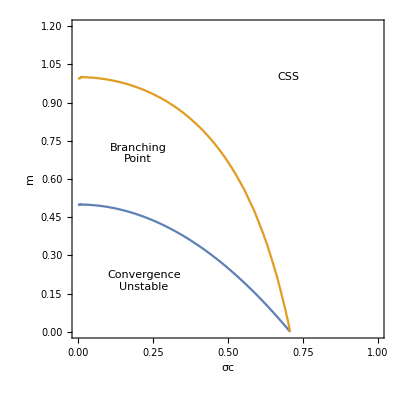

```mathematica
ContourPlot[{0==-2-(-1+m)/σc^2-m/σc^2,0==-2+m/σ^2-(-1+m)/σc^2},{σc,0,1},{m,0,1.2},FrameLabel->{"σc","m"},
Epilog->{Text["CSS",{0.7,1.0}],Text["Branching\nPoint",{0.2,0.7}],Text["Convergence\nUnstable",{0.22,0.2}]}]
```

The one-prey one-predator equilibrium should be evolutionarily stable above the golden line and convergence stable above the blue line.  That implies that branching point happens before coevolutionary cycles as m decreases.  Let's verify numerically.

{-4.,-2.}

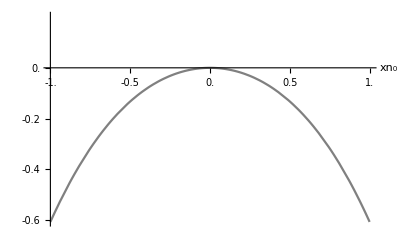

```mathematica
(* convergence & evolutionarily stable = CSS *)
σc=0.5;
m=1;
eq=FindEcoEvoEq[{Subscript[xn, 1]->0,Subscript[xp, 1]->0,Subscript[n, 1]->0.1,Subscript[p, 1]->1}];
EvoEigenvalues[eq]
PlotInv[eq,{Subscript[xn, 0],-1,1}]
```

{-1.4+1.68523 ⅈ,-1.4-1.68523 ⅈ}

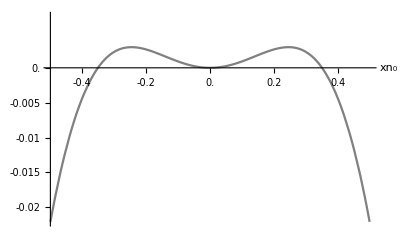

```mathematica
(* convergence, but not evolutionarily, stable = Branching Point *)
σc=0.5;
m=0.6;
eq=FindEcoEvoEq[{Subscript[xn, 1]->0,Subscript[xp, 1]->0,Subscript[n, 1]->0.1,Subscript[p, 1]->1}];
EvoEigenvalues[eq]
PlotInv[eq,{Subscript[xn, 0],-0.5,0.5}]
```

{0.2+1.249 ⅈ,0.2-1.249 ⅈ}

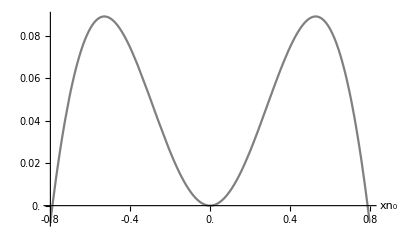

```mathematica
(* neither convergence nor evolutionarily stable (oscillatory) *)
σc=0.5;
m=0.2;
eq=FindEcoEvoEq[{Subscript[xn, 1]->0,Subscript[xp, 1]->0,Subscript[n, 1]->0.1,Subscript[p, 1]->1}];
EvoEigenvalues[eq]
PlotInv[eq,{Subscript[xn, 0],-0.8,0.8}]
```

Let's see the eco-evolutionary dynamics with EcoEvoSim, setting trait variances small to separate ecological and evolutionary timescales:

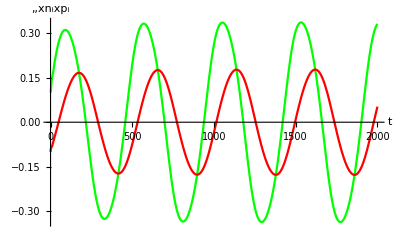

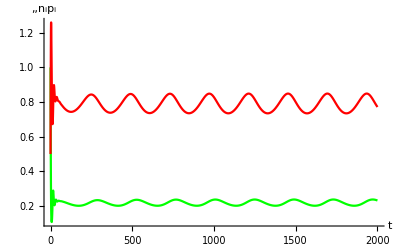

```mathematica
tmax=2000;
sol=EcoEvoSim[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5},{V[xn]->0.01,V[xp]->0.01},tmax];
PlotDynamics[sol,{xn,xp}]
PlotDynamics[sol,{n,p}]
```

Make an evolutionary phase plane diagram and superimpose the predator-prey coevolutionary cycle:

```mathematica
eq11=SolveEcoEq[{Subscript[𝒩, n]->1,Subscript[𝒩, p]->0}]⟦-1⟧;
eq12=SolveEcoEq[{Subscript[𝒩, n]->0,Subscript[𝒩, p]->1}]⟦-1⟧;
eq2=SolveEcoEq[{Subscript[𝒩, n]->1,Subscript[𝒩, p]->1}]⟦-1⟧;
Show[
PlotEvoPhasePlane[{eq11,eq12},eq2,{Subscript[xn, 1],-1,1},{Subscript[xp, 1],-1.4,1.4}],
RuleListPlot[sol,{xn,xp},PlotStyle->Pink]
]
```

-Graphics-

Changing the trait variances in different guilds can affect convergence stability.  Faster predator evolutionary rates can (convergence) stabilize the eco-evolutionary equilibrium:

```mathematica
EvoEigenvalues[eq,{V[xn]->0.01,V[xp]->0.1}]
```

{-0.034+0.0210713 ⅈ,-0.034-0.0210713 ⅈ}

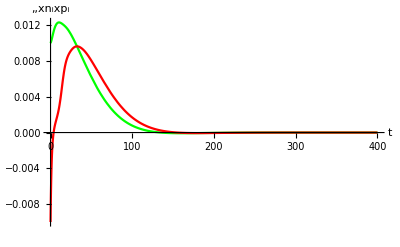

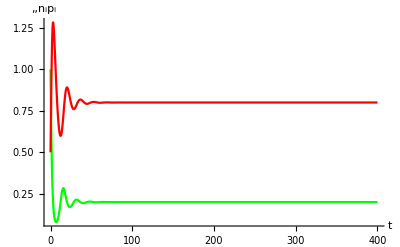

```mathematica
tmax=400;
sol=EcoEvoSim[{Subscript[xn, 1]->0.01,Subscript[xp, 1]->-0.01},{Subscript[n, 1]->1,Subscript[p, 1]->0.5},{V[xn]->0.01,V[xp]->0.1},tmax];
PlotDynamics[sol,{xn,xp}]
PlotDynamics[sol,{n,p}]
```

Nevertheless, the prey in this equilibrium are still not evolutionarily stable:

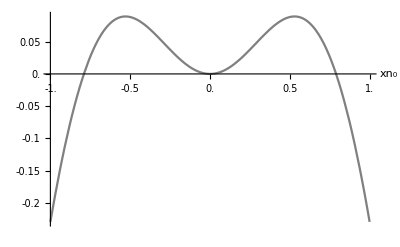

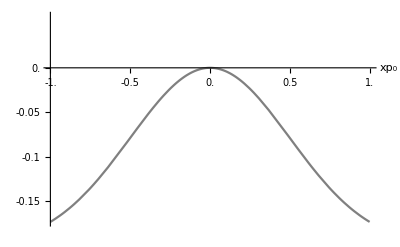

```mathematica
PlotInv[FinalSlice[sol],{Subscript[xn, 0],-1,1}]
PlotInv[FinalSlice[sol],{Subscript[xp, 0],-1,1}]
```

Let's look for a two-prey, one-predator eco-evolutionary equilibrium:

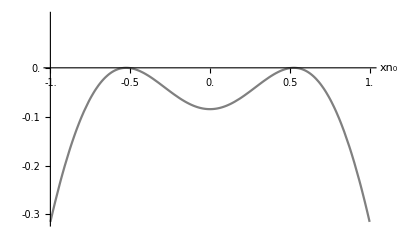

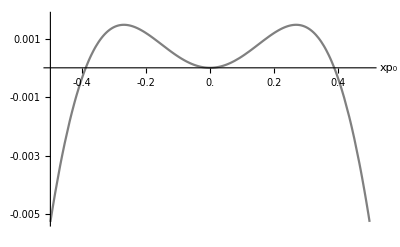

```mathematica
eq=FindEcoEvoEq[{Subscript[xn, 1]->-0.3,Subscript[xn, 2]->0.3,Subscript[xp, 1]->0},{Subscript[n, 1]->0.2,Subscript[n, 2]->0.2,Subscript[p, 1]->0.5}];
PlotInv[eq,{Subscript[xn, 0],-1,1}]
PlotInv[eq,{Subscript[xp, 0],-0.5,0.5}]
```

Now the prey are evolutionarily stable but the predators aren't.  How about two prey and two predators?

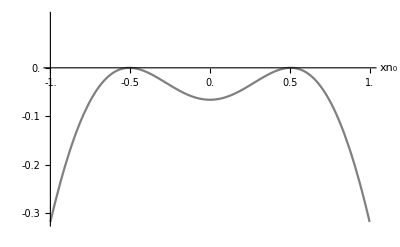

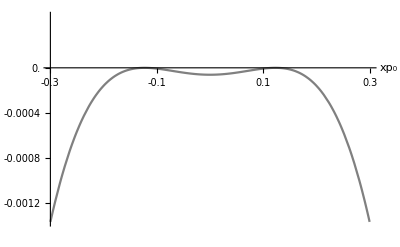

```mathematica
eq=FindEcoEvoEq[{Subscript[xn, 1]->-0.5,Subscript[xn, 2]->0.5,Subscript[xp, 1]->-0.5,Subscript[xp, 2]->0.5},{Subscript[n, 1]->0.2,Subscript[n, 2]->0.2,Subscript[p, 1]->0.5,Subscript[p, 2]->0.5}];
PlotInv[eq,{Subscript[xn, 0],-1,1}]
PlotInv[eq,{Subscript[xp, 0],-0.3,0.3}]
```

Looks uninvasible.  Check with GlobalESSQ:

```mathematica
GlobalESSQ[eq]
```

{{True,True},{{0.,{xn→-0.5051}},{1.38778×10^-17,{xp→0.123004}}}}

Also, check convergence stability with EvoEigenvalues:

```mathematica
EvoEigenvalues[eq]
```

{-1.92213,-1.72105,-0.238493,-0.0333106}

Simulate eco-evolutionary dynamics with EcoEvoSim, starting with all species close together and far from x=0:

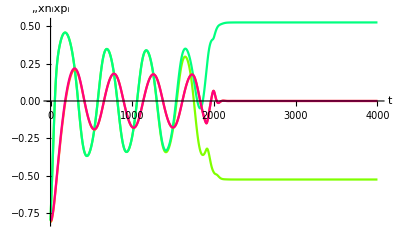

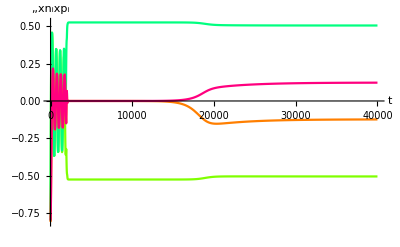

```mathematica
tmax=40000;
sol=EcoEvoSim[{Subscript[xn, 1]->-0.801,Subscript[xn, 2]->-0.8,Subscript[xp, 1]->-0.81,Subscript[xp, 2]->-0.8},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5,Subscript[p, 1]->0.1,Subscript[p, 2]->0.1},{V[xn]->0.01,V[xp]->0.01},tmax];
PlotDynamics[Slice[sol,{0,4000}],{xn,xp}]
PlotDynamics[sol,{xn,xp}]
```

First the species converge towards the one-prey, one-predator coevolutionary cycle.  Around t=2000, the prey branch and the system reaches the unstable two-prey, one-predator equilibrium.  This is marginally unstable, so it takes until t=16000 for the predators to branch and approach the final stable two-prey, two-predator ESS.

Related Tutorials

ExampleModels